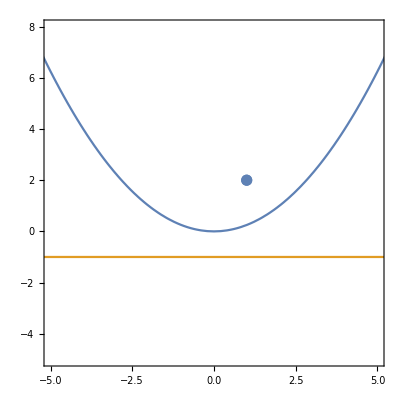

```mathematica
SetDirectory[NotebookDirectory[]];
f1=0;f2=1;
a=0;b=1;c=1;
Show[
ContourPlot[{
(a x+b y+c)^2/(a^2+b^2)==(x-f1)^2+(y-f2)^2,
a x+b y+c==0
},{x,-10,10},{y,-10,10},PlotPoints->50],
ListPlot[{{1,2}},PlotStyle->PointSize[0.02]],
PlotRange->{{-5,5},{-5,8}},
Axes->None,AspectRatio->1
]
```

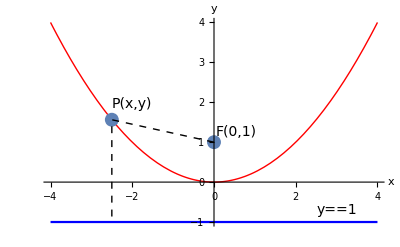

```mathematica
x0=-2.5;
y0=x0^2/4;
Show[
Plot[{x^2/4,-1},{x,-4,4},PlotStyle->{{Thick,Red},{Blue}}],
ListPlot[{{0,1},{x0,x0^2/4}},PlotStyle->PointSize[0.025]],
Graphics[{Dashed,Line[{{0,1},{x0,x0^2/4},{x0,-1}}]}],
AxesLabel->{x,y},AxesStyle->Directive[14],
Epilog->{
Text[Style[TraditionalForm[HoldForm[P[x,y]]],14],{x0+0.5,y0+0.4}],Text[Style[TraditionalForm[HoldForm[F[0,1]]],14],{0+0.55,1+0.25}],
Text[Style[TraditionalForm[HoldForm[y==1]],14],{3,-1+0.3}],
}
]
Export[{"parabola1.svg","parabola1.pdf"},%];
```

```mathematica
(-1/2+3)/2
```

5/4

```mathematica
-2x^2+5x+3/.x->5/4
```

49/8

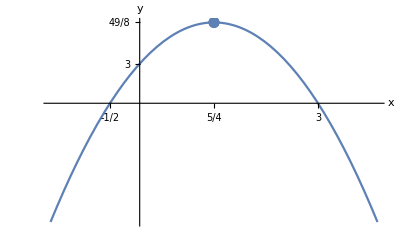

{parabola2.pdf,parabola2.svg}

```mathematica
Show[Plot[-2x^2+5x+3,{x,-1.5,4}],
ListPlot[{{5/4,49/8}},PlotStyle->PointSize[0.02]],
Ticks->{{-1/2,5/4,3},{3,49/8}},AxesLabel->{x,y},AxesStyle->Directive[14]
]
Export[{"parabola2.pdf","parabola2.svg"},%]
```